# Omid Amir Index

## Slide Show Subtitle

Baoxiang Pan
8.7.2017

## Materials

```mathematica
precip=Import["/Users/lambda/Documents/Wolfram Mathematica/Omid-Amir-Index/data/CAMonthTotal.txt","List"];
```

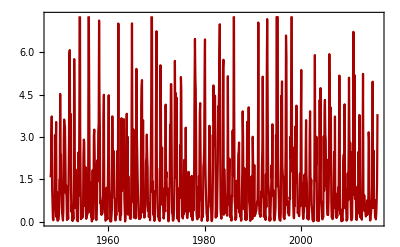

```mathematica
DateListPlot[TimeSeries[precip,{{1948,1,1},Automatic,"Month"}]]
```

```mathematica
wprecip=Table[Total[precip[[10+year;;15+year]]],{year,0,Length[precip]/12}];
Length[wprecip]
```

69

## Numerical Experiments

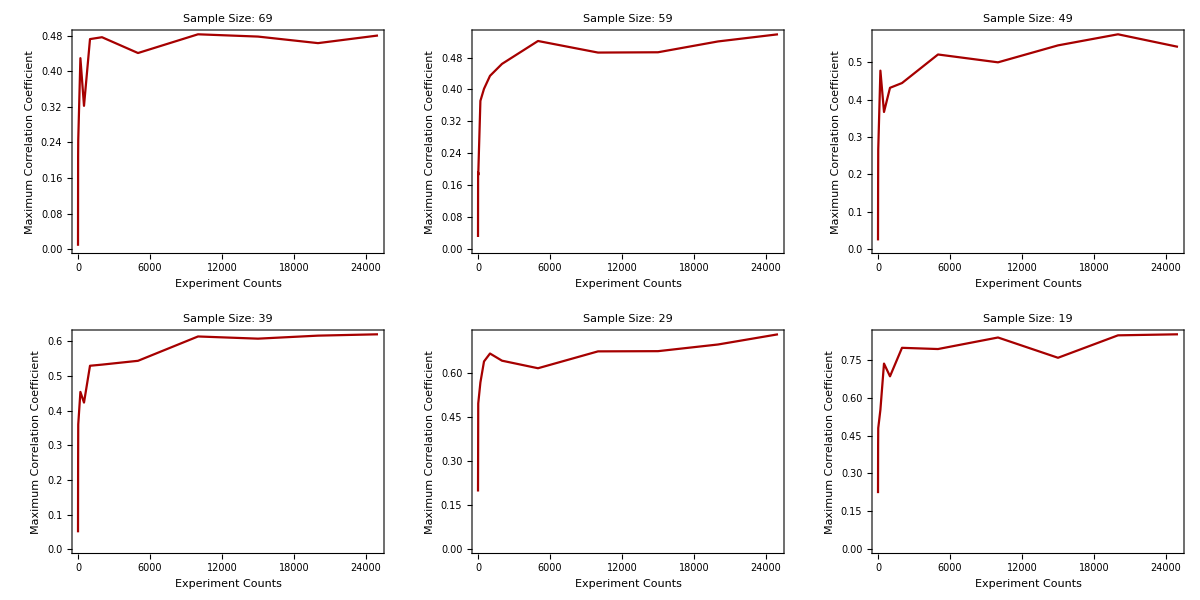

```mathematica
Grid[ArrayReshape[Table[Block[{sprecip=wprecip[[point-1947;;]]},
ListLinePlot[Table[{sample,Max[Table[Abs[Correlation[RandomReal[{0,1},Length[sprecip]],sprecip]],{i,sample}]]},
	{sample,{1,10,20,200,500,1000,2000,5000,10000,15000,20000,25000}}],
	ImageSize->400,
	PlotLabel->"Sample Size: "<>ToString[2017-point],
	Frame->True,BaseStyle->13,FrameLabel->{"Experiment Counts","Maximum Correlation Coefficient"}]],
	{point,1948,1998,10}],{2,3}]]
```